```mathematica
<<PlotLegends`
```

```mathematica
c = 2.997 10^8;hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
ω = c 2 Pi/λ;
λLat = 532 10^-9;
Γ = 1.84 10^6;
ωLat = c * 2 Pi / (λLat);
IntensityLat = 1 /(10^-4);(*from other simulation*)
kb = 1.38066 10^-23;
ω0 = 1.3 10^6;
Ωfree = 2 Pi 30.6 10^3;
ΩRm1 = Sqrt[2 Pi 30.6 10^3];
ΩRm2 = Sqrt[2 Pi 30.6 10^3];
ΔRm = 10^9;
ΔR = 10^12;
(*lattice params*)
a = 532 10^-9;
σ = 0.1 *3 * (265 10^-12)^2/(2 Pi);
ρ = 1/a^2;
RCs = 500;
```

```mathematica
Dr[n_,nt_]:= √((n!)/((n+nt-n)!))(ⅈ η 1)^(nt-n)LaguerreL[n,nt-n,(η 1)^2 Exp[-η^2/2]]
```

```mathematica
Calculation of Scattering Rates Γeff(n)
```

```mathematica
Clear[P1list,P2list];
P1list = {};
P2list = {};
P3list = {};
tab = Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
Int = 0.6 10^-3/(10^-4);
h = 2 Pi *hbar;
;ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];

H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun3=ρ33/.First[sol];
fun1=ρ11/.First[sol];
fun2 = ρ22 /. First[sol];
expsol = Solve[Re[fun3[4 10^-5  ]] == Re[fun3[1 10^-5 ]] Exp[-l 3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
AppendTo[P1list, Re[fun1[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
AppendTo[P2list, Re[fun2[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
AppendTo[P3list, Re[fun3[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
{n,lam},{n,0,10}]
Γscatt = tab[[All, 2]]
P1list
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

{{0,0},{1,110523.},{2,197506.},{3,263076.},{4,312546.},{5,350295.},{6,379048.},{7,400582.},{8,416461.},{9,428193.},{10,437443.}}

{0,110523.,197506.,263076.,312546.,350295.,379048.,400582.,416461.,428193.,437443.}

{1.,0.839578,0.721808,0.63515,0.567144,0.512049,0.470312,0.443034,0.42778,0.418109,0.406279}

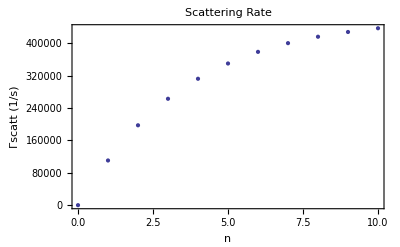

```mathematica
ListPlot[tab, FrameLabel-> {"n","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate", Frame-> True]
```

```mathematica
(Plots: Scattering Rate As a Function of Raman and Repump Coupling strengths.)
```

```mathematica
tabrepump =Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
(*ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];*)
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-5}, MaxSteps-> 1000000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[8 10^-5  ]] == Re[fun[5 10^-5 ]] Exp[-l  3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{ΩR,lam},{ΩR,0,4 10^6, 0.5 10^5}],{n,1,10}];
```

Set::write: Tag Times in 0\ 485760. is Protected.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Times in 0\ 485760. is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

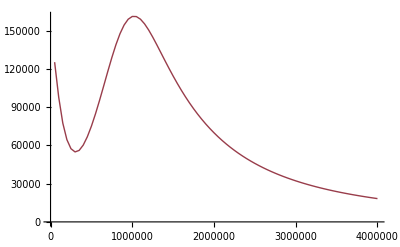
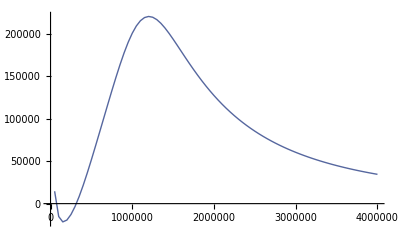
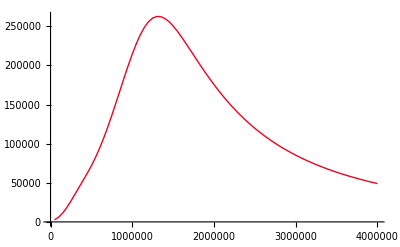
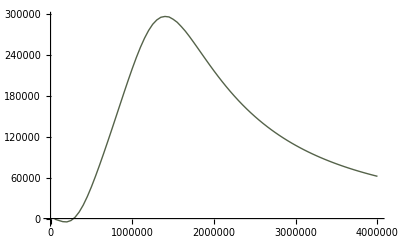
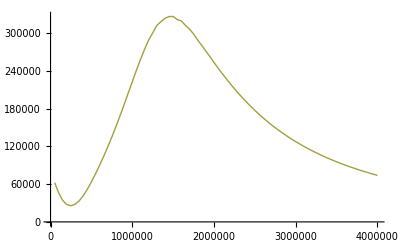
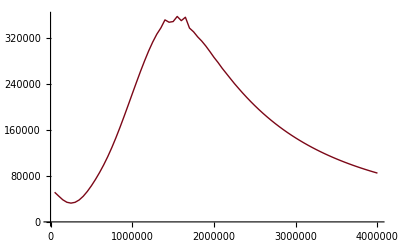
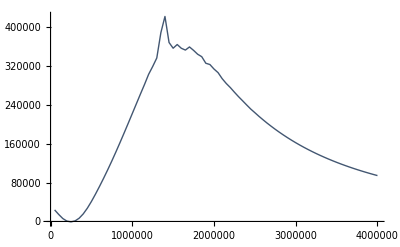
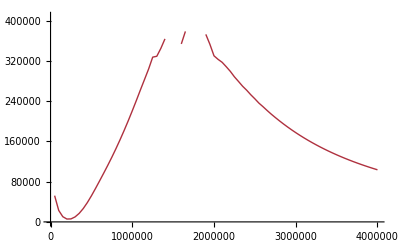

```mathematica
repumplots = Table[ListLinePlot[tabrepump[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

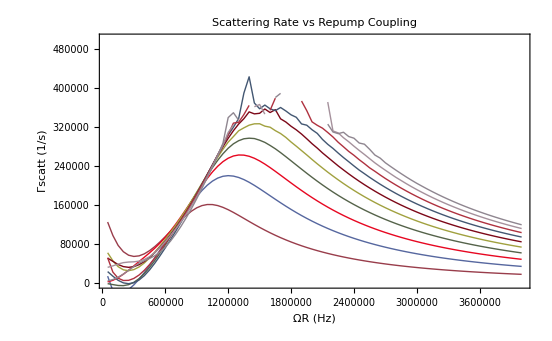

```mathematica
Show[repumplots , PlotRange -> {All,{0,500000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
tabraman=Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
(*Ω1 = 50 2 Pi 10^3;*)
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[10 10^-5  ]] == Re[fun[3 10^-5 ]] Exp[-l  7 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{Ω1,lam},{Ω1,0,2.5 10^6, 2 10^4}],{n,1,10}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00730591.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00719219.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00706502.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

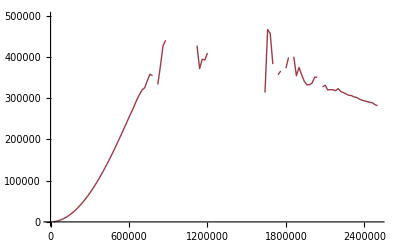
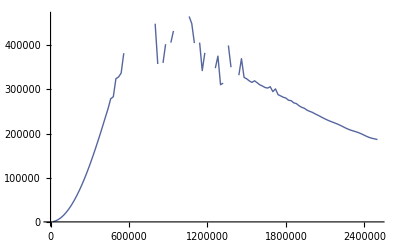
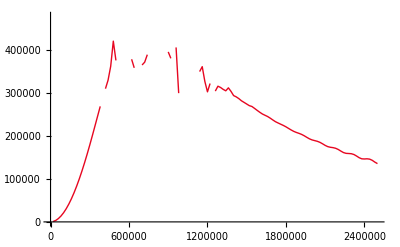
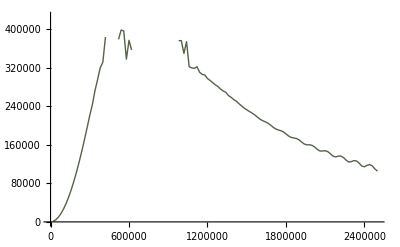
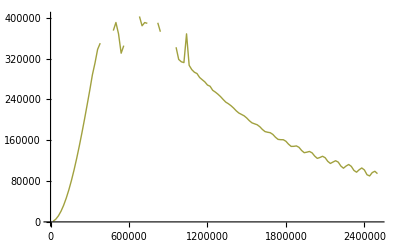
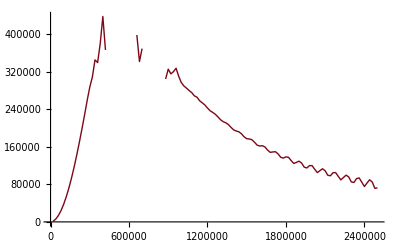
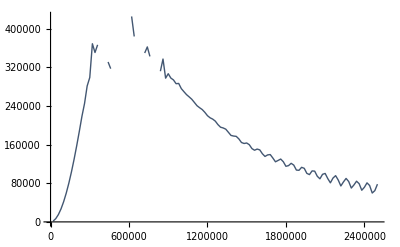
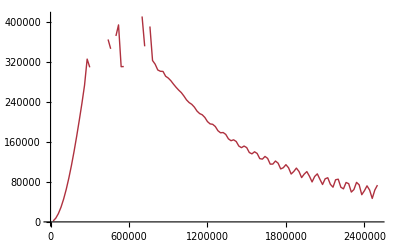

```mathematica
ramanplots = Table[ListLinePlot[tabraman[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

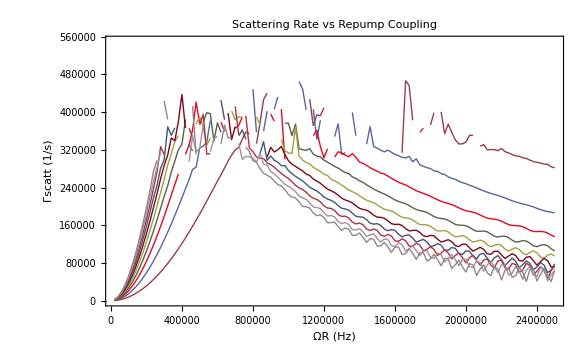

```mathematica
Show[ramanplots , PlotRange -> {All,{0,550000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
Photon recoil
```

```mathematica
Γscatt
```

{0,110523.,197506.,263076.,312546.,350295.,379048.,400582.,416461.,428193.,437443.}

```mathematica
pphoton = h / λ
```

1.45459×10^-27

```mathematica
mCs = 132.90545 * 1.660539 10^-27 (*internet*)
```

2.20695×10^-25

```mathematica
Erecoil = pphoton^2/(2mCs)
```

4.7936×10^-30

```mathematica
Λreca= Γscatt * Erecoil;
Λrece= Γscatt * Erecoil;
```

```mathematica
Λrecarate= Γscatt * Erecoil    2/(3 kb) *10^3
Λrecerate= Γscatt * Erecoil    2/(3 kb) *10^3
```

{0.,25.582,45.7156,60.8927,72.3432,81.0809,87.7361,92.7204,96.3959,99.1113,101.252}

{0.,25.582,45.7156,60.8927,72.3432,81.0809,87.7361,92.7204,96.3959,99.1113,101.252}

```mathematica
Off-resonant scattering: Raman
```

```mathematica
λ
```

4.55527×10^-7

```mathematica
Ephoton = h * c/λ
```

4.35942×10^-19

```mathematica
ΛscRm =Table[ Γ    (ΩRm1^2 + ΩRm2^2)/(4 ΔRm^2) Ephoton ,{n,1,10}] 2/(3 kb)10^3
```

{3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234}

```mathematica
Off-resonant scattering: Repump beam
```

```mathematica
ΛscRp = P1list* Γ ΩR^2/(4 ΔR^2)Ephoton 2/(3 kb)10^3
```

{24.2951,20.3976,17.5364,15.431,13.7788,12.4403,11.4263,10.7636,10.3929,10.158,9.87058}

```mathematica
Lattice beams
```

```mathematica
(*ephoton not precise, should be average over all resonances*)
(*numerical value taken from last weeks simulartion*)
```

```mathematica
ΛscLat =  Table[1.00217872738179 10^-9 * IntensityLat 2*hbar ω 2/(3 kb) *10^3 ,{n,1,10}]
```

{421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916}

```mathematica
Off-Res Raman Couplings: Carrier transitions n-> n
```

```mathematica
Ωcarrier = Table[Ω1 (1-0.5 η^2(2n+1)),{n,1,10}]
```

{295310.,282743.,270177.,257611.,245044.,232478.,219911.,207345.,194779.,182212.}

```mathematica
Λcarrier = Table[P1list[[n]] ΩR^2/Γ Ωcarrier[[n]]^2/(4 ω0^2),{n,1,10}]2*Erecoil 2/(3 kb) *10^3
```

{8.14357,6.26766,4.92014,3.93607,3.1801,2.58425,2.12394,1.77863,1.51552,1.2963}

```mathematica
Off-Res Raman Couplings: Blue transitions
```

```mathematica
Ωblue = Table[Ω1 (Sqrt[n+1]),{n,1,10}]//N;
```

```mathematica
Λblue= Table[P1list[[n]] ΩR^2/Γ Ωblue[[n]]^2/(16 ω0^2),{n,1,10}]hbar ω0 2/(3 kb) *10^3
```

{65.8957,82.9868,95.128,104.634,112.117,118.096,123.966,131.373,140.944,151.533}

```mathematica
Off-Res Raman Couplings: Doubly red
```

```mathematica
Ωdoublyred= Table[Ωcarrier[[1]]*η^2*Sqrt[(n-1)*n],{n,1,10}]//N;
```

```mathematica
Λdoublyred = -Table[P1list[[n]] ΩR^2/Γ Ωdoublyred[[n]]^2/(4 ω0^2),{n,1,10}]hbar ω0 2/(3 kb) *10^3
```

{0.,-0.312863,-0.806929,-1.4201,-2.11342,-2.86217,-3.68042,-4.62262,-5.73872,-7.01123}

```mathematica
Rescattering
```

```mathematica
Λresc = Table[(P1list[[n]]α+P2list[[n]](1-α)) 1.00217872738179 10^9 (σ ρ)/2 Log[RCs],{n,1,10}]*2/(3 kb) *10^3 *2* Erecoil
```

{0.0102472,0.00929342,0.0085851,0.00806413,0.00765157,0.0073038,0.00702288,0.00682686,0.00671841,0.00667167}

```mathematica
Repumping of state 2
```

```mathematica
Γ2s = ΩR^2 Γ/(Γ^2+4 δ2^2);
ΛRepump = Table[P2list[[n]] * Γ2s *2* Erecoil,{n,1,10}] 2/(3 kb) *10^3
```

{0.,63.7699,109.833,143.748,170.02,190.053,203.614,211.331,215.754,220.592}

```mathematica
Cooling Rate
```

```mathematica
Λcool = -Table[P3list[[n]] α Abs[Dr[n-1,n-1]]^2*Γ,{n,1,10}] 2/(3 kb) *10^3 hbar ω0
```

{0.,-400.743,-647.852,-784.36,-858.832,-899.499,-911.754,-892.408,-842.502,-771.622}

```mathematica
Generate table
```

```mathematica
TableOfValues2=MapThread[Prepend,{{{"n = 1","n=2","n=3","n=4","n=5","n=6","n=7","n=8","n=9","n=10"},Λrecarate, Λrecerate,Λcarrier ,Λblue  ,ΛscRm ,ΛscRp ,Λresc,ΛscLat, Λdoublyred,Λcool},{"μK/ms","Λrecarate", "Λrecerate","Λcarrier" ,"Λblue"  ,"ΛscRm" ,"ΛscRp" ,"Λresc","ΛscLat","Λdoublyred","Λcool"}}];
```

```mathematica
Grid[TableOfValues2[[All,{1,2,4,6,8,10}]],ItemStyle->{Automatic,{1->{Bold,14}}},Frame->{All,1->True},Background->{None,{{LightOrange,LightGray}}}]
```

μK/ms | n = 1 | n=3 | n=5 | n=7 | n=9
Λrecarate | 0. | 45.7156 | 72.3432 | 87.7361 | 96.3959
Λrecerate | 0. | 45.7156 | 72.3432 | 87.7361 | 96.3959
Λcarrier | 8.14357 | 4.92014 | 3.1801 | 2.12394 | 1.51552
Λblue | 65.8957 | 95.128 | 112.117 | 123.966 | 140.944
ΛscRm | 3.7234 | 3.7234 | 3.7234 | 3.7234 | 3.7234
ΛscRp | 24.2951 | 17.5364 | 13.7788 | 11.4263 | 10.3929
Λresc | 0.0102472 | 0.0085851 | 0.00765157 | 0.00702288 | 0.00671841
ΛscLat | 421.916 | 421.916 | 421.916 | 421.916 | 421.916
Λdoublyred | 0. | -0.806929 | -2.11342 | -3.68042 | -5.73872
Λcool | 0. | -647.852 | -858.832 | -911.754 | -842.502

```mathematica
Rate equation
```